```mathematica
f[x_,h_,r_] = h + x*(r-x)
```

h+(r-x) x

```mathematica
D[f]
```

f

```mathematica
f[x,h,r] = h+x*(r-x)
```

h+(r-x) x

```mathematica
D[f]
```

f

```mathematica
D[f[x,h,r]]
```

h+(r-x) x

```mathematica
D[f[x,h,r],x]
```

r-2 x

```mathematica
f' =r-2 x
```

```mathematica
r-2 x
```

```mathematica
f'[x,h,r]
```

(r-2 x)[x,h,r]

```mathematica
Solve[{f[x,h,r] == 0, f' == 0},x]
```

{}

```mathematica
Solve[{f[x,h,r] == 0, f' == 0},{h,r}]
```

```mathematica
{{h->-x^2,r->2 x}}

NSolve[{f[x,h,r] == 0, f' == 0},{h,r}]
```

{{h→-x^2,r→2 x}}

```mathematica
{{h->-1. x^2,r->2. x}}
h = -(r/2)^2
```

{{h→-1. x^2,r→2. x}}

-r^2/4

```mathematica
h[r] = -(r/2)^2
```

Set::write: Tag Times in (-r^2/4)[r] is Protected.

-r^2/4

```mathematica
Plot[h[r], {r, -10, 10}]
```

-Graphics-

```mathematica
h[r]
```

(-r^2/4)[r]

```mathematica
temp[r] = -(r/2)^2
```

-r^2/4

```mathematica
Plot[temp[r], {r, -10,10}]
```

-Graphics-

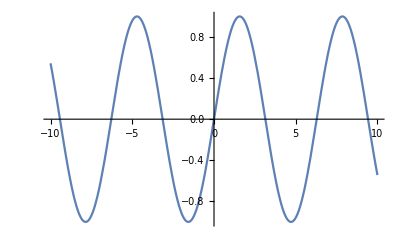

```mathematica
Plot[Sin[x],{x,-10,10}]
```

```mathematica
Solve[f[x,h,r] == 0, x]
```

{{x→r/2},{x→r/2}}

```mathematica
f[x,h,r] = h+x*(r-x)
```

h+(r-x) x

```mathematica
Solve[f[x,h,r] == 0, x]
```

```mathematica
{{x->1/2 (r-√(4 h+r^2))},{x->1/2 (r+√(4 h+r^2))}}
x1 = 1/2 (r-√(4 h+r^2))
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

1/2 (r-√(4 h+r^2))

```mathematica
f'[x,h,r] = D[f[x,h,r], x]
```

```mathematica
r-2 x
```

r-2 x

```mathematica
x2 = 1/2 (r+√(4 h+r^2))
x1
```

1/2 (r+√(4 h+r^2))

1/2 (r-√(4 h+r^2))

```mathematica
Solve[{f[x1,h,r] == 0, f'[x1,h,r] == 0}, {h,r}]
```

Solve[{f[1/2 (r-√(4 h+r^2)),h,r]==0,f'[1/2 (r-√(4 h+r^2)),h,r]==0},{h,r}]

```mathematica
f[x,h,r]
```

h+(r-x) x

```mathematica
f[x1,h,r]
```

f[1/2 (r-√(4 h+r^2)),h,r]

```mathematica
x = x1
```

1/2 (r-√(4 h+r^2))

```mathematica
f[x,h,r]
```

f[1/2 (r-√(4 h+r^2)),h,r]

```mathematica
Unset[x]
```

```mathematica
f(x1,h,r)
```

```mathematica
f[x,h,r]
```

h+(r-x) x

```mathematica
x = x1
```

1/2 (r-√(4 h+r^2))

```mathematica
f(x,h,r)
```

```mathematica
Unset[x]
```

```mathematica
x=2
```

2

```mathematica
f(x,h,r)
```

```mathematica
Unset[x]
```

```mathematica
f[x1,h,r]
```

```mathematica
f[1/2 (r-√(4 h+r^2)),h,r]
```

f[1/2 (r-√(4 h+r^2)),h,r]

```mathematica
f(x1,h,r)
```

```mathematica
Evaluate[f[x,h,r], x = x1]
```

Sequence[h+1/2 (r-√(4 h+r^2)) (r+1/2 (-r+√(4 h+r^2))),1/2 (r-√(4 h+r^2))]

```mathematica
Simplify[Evaluate[f[x,h,r], x = x1]]
```

f[True,h,r]

```mathematica
Sin(x1)
```

1/2 (r-√(4 h+r^2)) Sin

```mathematica
Sin[x1]
```

Sin[1/2 (r-√(4 h+r^2))]

```mathematica
N[Sin[x1]]
```

Sin[0.5 (r-1. √(4. h+r^2))]

```mathematica
f[x_,h_,r_]=h+x*(r-x)
```

h+(r-x) x

```mathematica
f'[x_,h_,r_]=D[f[x_,h_,r_],x]
```

Rule::rhs: Pattern r_ appears on the right-hand side of rule f'[x_,h_,r_]→(r_-x_) Pattern^(1,0)[x,_]-x_ Pattern^(1,0)[x,_].

Rule::rhs: Pattern x_ appears on the right-hand side of rule f'[x_,h_,r_]→(r_-x_) Pattern^(1,0)[x,_]-x_ Pattern^(1,0)[x,_].

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

(r_-x_) Pattern^(1,0)[x,_]-x_ Pattern^(1,0)[x,_]

```mathematica
D[f[x_,h_,r_],x]
```

(r_-x_) Pattern^(1,0)[x,_]-x_ Pattern^(1,0)[x,_]

```mathematica
D[f[x,h,r],x]
```

r-2 x

```mathematica
f[x_,h_,r_]:=h+x*(r-x)
```

```mathematica
f
```

f

```mathematica
f[x,h,r]
```

h+(r-x) x

```mathematica
D[f[x,h,r],x]
```

r-2 x

```mathematica
f'[x_,h_,r_]:=D[f[x,h,r],x]
```

```mathematica
f'[x,h,r]
```

r-2 x

```mathematica
Solve[f[x,h,r]==0]
```

{{h→-r x+x^2}}

```mathematica
Solve[f[x,h,r] == 0, x]
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

```mathematica
x1=1/2 (r-√(4 h+r^2))
```

1/2 (r-√(4 h+r^2))

```mathematica
x2 = 1/2 (r+√(4 h+r^2))
```

1/2 (r+√(4 h+r^2))

```mathematica
f[x1,h,r]
```

h+1/2 (r-√(4 h+r^2)) (r+1/2 (-r+√(4 h+r^2)))

```mathematica
Solve[{f[x1,h,r] == 0, f'[x1,h,r]==0},{h,r}]
```

{}

```mathematica
f'[x1,h,r]
```

∂_(1/2 (r-√(4 h+r^2))) (h+1/2 (r-√(4 h+r^2)) (r+1/2 (-r+√(4 h+r^2))))

```mathematica
f_prime[x_,h_,r_]:=D[f[x,h,r],x]
```

```mathematica
f_prime[x,h,r]
```

f_prime[x,h,r]

```mathematica
D[f[x,h,r],x]
```

r-2 x

```mathematica
f_prime[x_,h_,r_] = r-2x
```

r-2 x

```mathematica
f[x,h,r]
```

h+(r-x) x

```mathematica
f_prime[x,h,r]
```

f_prime[x,h,r]

```mathematica
f_prime[x_,h_,r_] := r-2*x
```

```mathematica
f_prime[x,h,r]
```

f_prime[x,h,r]

```mathematica
f_prime[x_,h_,r_]:=r-2x
```

```mathematica
f_prime
```

f_prime

```mathematica
f_prime[x,h,r]
```

f_prime[x,h,r]

```mathematica
fprime[x_,h_,r_]:=r-2*x
```

```mathematica
fprime[x,h,r]
```

r-2 x

```mathematica
Solve[{f[x1,h,r]==0, fprime[x1,h,r]==0},{h,r}]
```

{{h→-r^2/4}}

```mathematica
h=-r^2/4
```

-r^2/4

```mathematica
h
```

-r^2/4

```mathematica
h[r_]:=-r^2/4
```

$Failed

```mathematica
h[r_]:=-(r^2)/4
```

$Failed

```mathematica
h[r_]:=-(r/4)^2
```

$Failed

```mathematica
h[r_]:=-r
```

```mathematica
$Failed

Plot[-r^2/4,{r,-10,10}]
```

$Failed

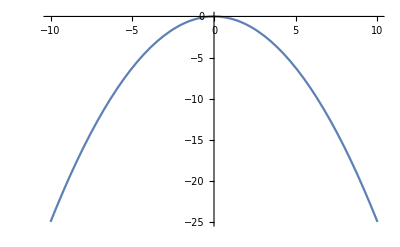
```mathematica
-Graphics-
Plot[f[x,h,r],{x,-10,10}]
```

-Graphics-

```mathematica
-Graphics-

f[x,h,r]
```

-Graphics-

-r^2/4+(r-x) x

```mathematica
f[x_,h_,r_]:=h+x*(r-x)
```

```mathematica
Plot[f[x,h,r], {x,-10,10}]
```

-Graphics-

```mathematica
Plot[f[x,h,r], {x,-10,10}, {r,-10,-10}]
```

Plot[f[x,h,r],{x,-10,10},{r,-10,-10}]

```mathematica
f[x,h,r]
```

-r^2/4+(r-x) x

```mathematica
h=h
```

-r^2/4

```mathematica
f[x_,h_,r_]:=h+x*(r-x)
```

```mathematica
Plot[f[x,h,r],{x,-10,10}]
```

-Graphics-

0

0

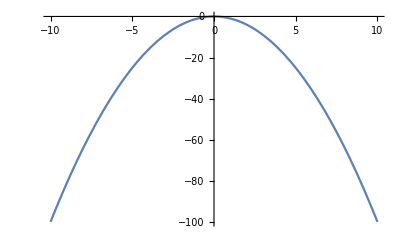

```mathematica
r= 0
h= 0
Plot[f[x,h,r],{x,-10,10}]
```

-10

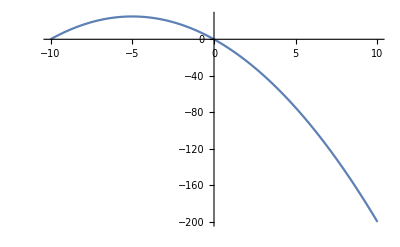

```mathematica
r= -10
Plot[f[x,h,r],{x,-10,10}]
```

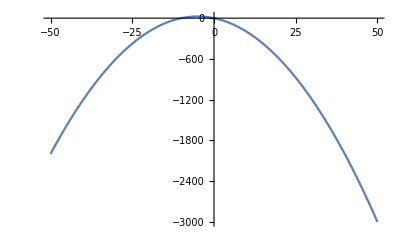

```mathematica
Plot[f[x,h,r],{x,-50,50}]
```

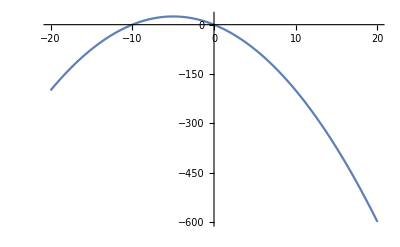

```mathematica
Plot[f[x,h,r],{x,-20,20}]
```

```mathematica
r= 10
```

10

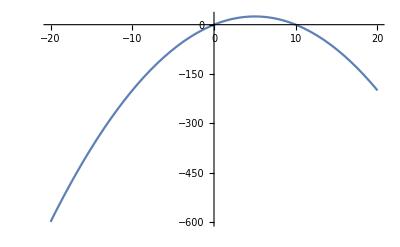

```mathematica
Plot[f[x,h,r],{x,-20,20}]
```